# Form factors for nuclide-photon interactions in the production of low-mass final states

As given in :

Improved Weizsäcker - Williams Method and Its Application to Lepton and W - Boson Pair Production
Kwang Je Kim and Yung - Su Tsai
1973
Phys. Rev. D 8, 3109

See also Appendix A of 0906.0580 (henceforth BEST in reference to the authors):

New fixed - target experiments to search for dark gauge forces
James D.Bjorken, Rouven Essig, Philip Schuster, and Natalia Toro
2009
Phys.Rev.D 80, 075018

We are testing against the results of the BEST paper

## Setup

```mathematica
$DirectorySetup="/Users/sam/Documents/Research/BeamDumpBSM/setup/directories.m";
Get[$DirectorySetup]
```

```mathematica
Get[$lowMassFormFactors]
```

0.71

#### Nuclear Parameters

```mathematica
(* Atomic Numbers *)
ZTungsten= 74;
ZAluminum= 13;

(* Mass Numbers *)
ATungsten= 183.84;
AAluminum= 26.982;
```

## Differential Plots (G_2)

#### Plotting: Tungsten

m_A = 500 Mev, E_0=10 GeV

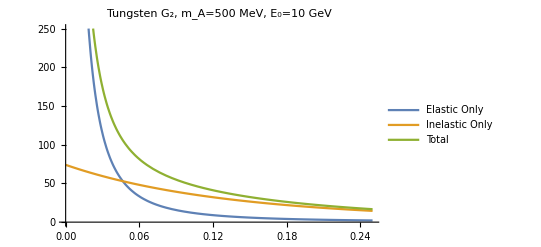

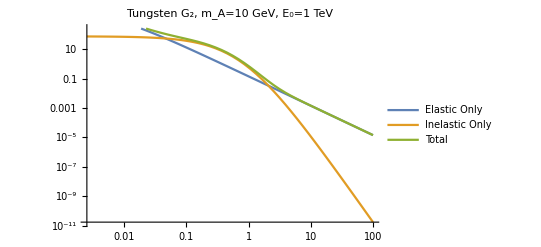

```mathematica
Plot[
{G2El[y,ZTungsten, ATungsten],G2In[y,ZTungsten, ATungsten],
G2El[y,ZTungsten, ATungsten]+G2In[y,ZTungsten, ATungsten]}, 
{y, tminapprox[mA, E0]/.{mA->.5, E0->10},
tmaxapprox[mA]/.{mA->.5}},
PlotLabel->"Tungsten G_2, m_A=500 MeV, E_0=10 GeV",
PlotLegends->{"Elastic Only", "Inelastic Only", "Total"},
PlotRange->{{0, tmaxapprox[mA]/.{mA->.5}}, {0, 250}}
]

LogLogPlot[
{G2El[y,ZTungsten, ATungsten],G2In[y,ZTungsten, ATungsten],
G2El[y,ZTungsten, ATungsten]+G2In[y,ZTungsten, ATungsten]}, 
{y, tminapprox[mA, E0]/.{mA->10, E0->1000},
tmaxapprox[mA]/.{mA->10}},
PlotLabel->"Tungsten G_2, m_A=10 GeV, E_0=1 TeV",
PlotLegends->{"Elastic Only", "Inelastic Only", "Total"},
PlotRange->{{0, tmaxapprox[mA]/.{mA->10}}, {0, 250}}
]
```

m_A = 100 Gev, E_0=1 TeV

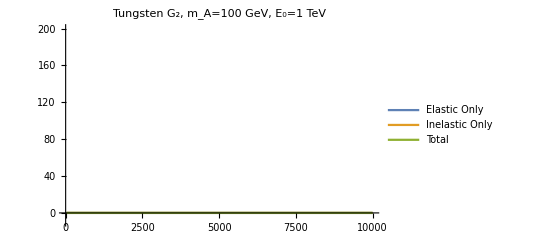

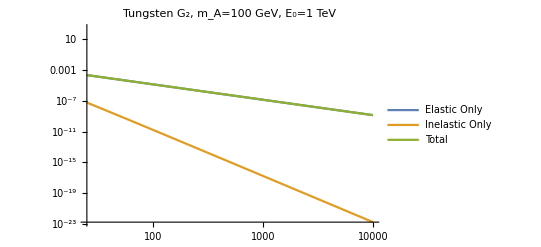

```mathematica
Plot[
{G2El[y,ZTungsten, ATungsten],G2In[y,ZTungsten, ATungsten],
G2El[y,ZTungsten, ATungsten]+G2In[y,ZTungsten, ATungsten]}, 
{y, tminapprox[mA, E0]/.{mA->100, E0->1000},
tmaxapprox[mA]/.{mA->100}},
PlotLabel->"Tungsten G_2, m_A=100 GeV, E_0=1 TeV",
PlotLegends->{"Elastic Only", "Inelastic Only", "Total"},
PlotRange->{{0, tmaxapprox[mA]/.{mA->100}}, {-10, 200}}
]

LogLogPlot[
{G2El[y,ZTungsten, ATungsten],G2In[y,ZTungsten, ATungsten],
G2El[y,ZTungsten, ATungsten]+G2In[y,ZTungsten, ATungsten]}, 
{y, tminapprox[mA, E0]/.{mA->100, E0->1000},
tmaxapprox[mA]/.{mA->100}},
PlotLabel->"Tungsten G_2, m_A=100 GeV, E_0=1 TeV",
PlotLegends->{"Elastic Only", "Inelastic Only", "Total"},
PlotRange->{{0, tmaxapprox[mA]/.{mA->100}}, {0, 250}}
]
```

#### Plotting: Aluminum

m_A = 500 Mev, E_0=10 GeV

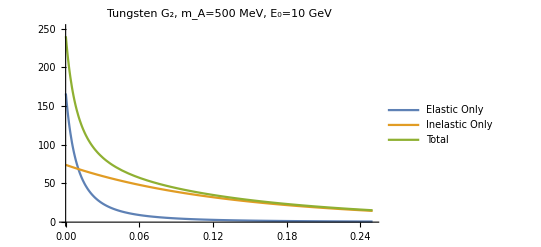

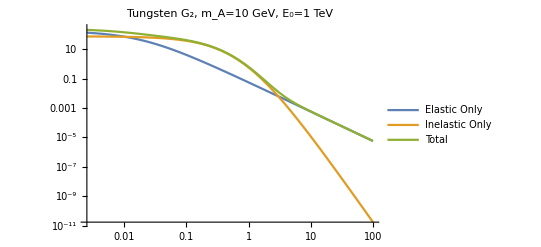

```mathematica
Plot[
{G2El[y,ZAluminum, AAluminum],G2In[y,ZTungsten, ATungsten],
G2El[y,ZAluminum, AAluminum]+G2In[y,ZTungsten, ATungsten]}, 
{y, tminapprox[mA, E0]/.{mA->.5, E0->10},
tmaxapprox[mA]/.{mA->.5}},
PlotLabel->"Tungsten G_2, m_A=500 MeV, E_0=10 GeV",
PlotLegends->{"Elastic Only", "Inelastic Only", "Total"},
PlotRange->{{0, tmaxapprox[mA]/.{mA->.5}}, {0, 250}}
]

LogLogPlot[
{G2El[y,ZAluminum, AAluminum],G2In[y,ZTungsten, ATungsten],
G2El[y,ZAluminum, AAluminum]+G2In[y,ZTungsten, ATungsten]}, 
{y, tminapprox[mA, E0]/.{mA->10, E0->1000},
tmaxapprox[mA]/.{mA->10}},
PlotLabel->"Tungsten G_2, m_A=10 GeV, E_0=1 TeV",
PlotLegends->{"Elastic Only", "Inelastic Only", "Total"},
PlotRange->{{0, tmaxapprox[mA]/.{mA->10}}, {0, 250}}
]
```

m_A = 100 Gev, E_0=1 TeV

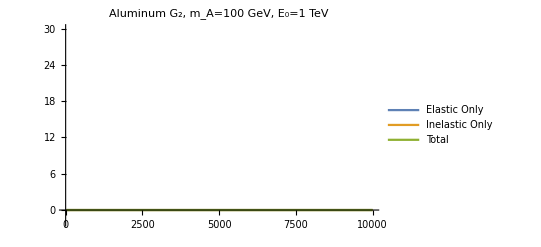

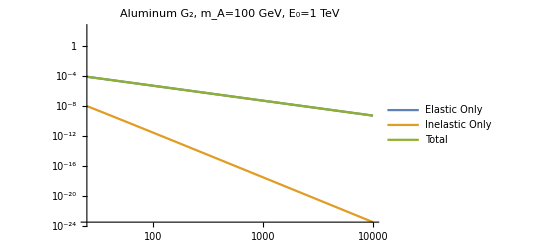

```mathematica
Plot[
{G2El[y,ZAluminum, AAluminum],G2In[y,ZAluminum, AAluminum],
G2El[y,ZAluminum, AAluminum]+G2In[y,ZAluminum, AAluminum]}, 
{y, tminapprox[mA, E0]/.{mA->100, E0->1000},
tmaxapprox[mA]/.{mA->100}},
PlotLabel->"Aluminum G_2, m_A=100 GeV, E_0=1 TeV",
PlotLegends->{"Elastic Only", "Inelastic Only", "Total"},
PlotRange->{{0, tmaxapprox[mA]/.{mA->100}}, {-2, 30}}
]

LogLogPlot[
{G2El[y,ZAluminum, AAluminum],G2In[y,ZAluminum, AAluminum],
G2El[y,ZAluminum, AAluminum]+G2In[y,ZAluminum, AAluminum]}, 
{y, tminapprox[mA, E0]/.{mA->100, E0->1000},
tmaxapprox[mA]/.{mA->100}},
PlotLabel->"Aluminum G_2, m_A=100 GeV, E_0=1 TeV",
PlotLegends->{"Elastic Only", "Inelastic Only", "Total"},
PlotRange->{{0, tmaxapprox[mA]/.{mA->100}}, {0, 250}}
]
```

#### Comments

The plots above show that the elastic form factor tends to be larger than the inelastic form factor in most of the parameter space when m_A is small. This seems  to be true independent of the value of E_0.

On the other hand, when m_A is larger, this is no longer the case: the inelastic component begins to be much larger everywhere in the parameter space. For this reason, for larger m_A, I believe the approximations used by BEST in the relevant part of their calculation break down rather dramatically.

## Integral Plots (χ)

### Analytic (using params from paper)

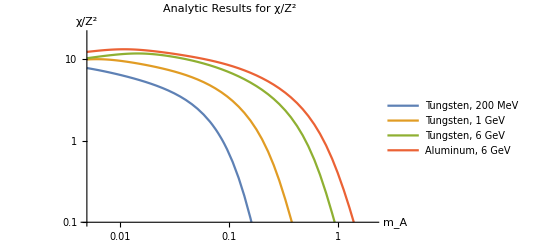

```mathematica
AnPaperPlot=LogLogPlot[
{χAn[ZTungsten,ATungsten,mA,.2]/ZTungsten^2,
χAn[ZTungsten,ATungsten,mA,1]/ZTungsten^2,
χAn[ZTungsten,ATungsten,mA,6]/ZTungsten^2,
χAn[ZAluminum,AAluminum,mA,6]/ZAluminum^2},
{mA,.005, 2.1},
PlotRange->{{.005, 2.1},{.1, 20}},
PlotLegends->{"Tungsten, 200 MeV", "Tungsten, 1 GeV", "Tungsten, 6 GeV","Aluminum, 6 GeV"},
PlotLabel->"Analytic Results for χ/Z^2",
AxesLabel->{Style["m_A",16],Style["χ/Z^2",16]}]
```

### Numerical (using params from paper)

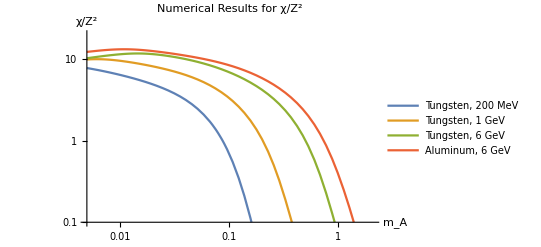

```mathematica
NumPaperPlot=LogLogPlot[
{χNum[ZTungsten,ATungsten,mA,.2]/ZTungsten^2,
χNum[ZTungsten,ATungsten,mA,1]/ZTungsten^2,
χNum[ZTungsten,ATungsten,mA,6]/ZTungsten^2,
χNum[ZAluminum,AAluminum,mA,6]/ZAluminum^2},
{mA,.005, 2.1},
PlotRange->{{.005, 2.1},{.1, 20}},
PlotLegends->{"Tungsten, 200 MeV", "Tungsten, 1 GeV", "Tungsten, 6 GeV","Aluminum, 6 GeV"},
PlotLabel->"Numerical Results for χ/Z^2",
AxesLabel->{Style["m_A",16],Style["χ/Z^2",16]}]
```

### Comparing Analytic and Numerical

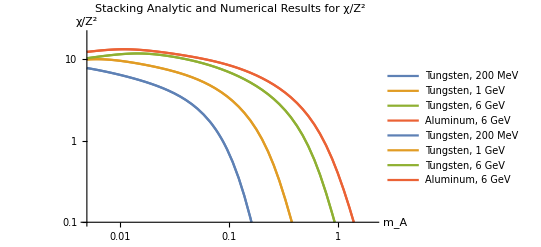

```mathematica
Show[AnPaperPlot,NumPaperPlot,
PlotLabel->"Stacking Analytic and Numerical Results for χ/Z^2"]
```

#### Comparison of the two

Plot some simple params

Easy way? Save the two plots and then plot individually above _and_ stack them down here?

Plot params used in paper

## Comparison to B.E.S.T.

### Web Plot Digitization (WPD) of B.E.S.T. Figure 10

Web plot digitized data

```mathematica
(* Tungsten, 200 MeV *)
BESTLogTungsten200MeVxvals={0.005032683,0.005326215,0.005636868,0.00596564,0.006313588,0.006681829,0.007071549,0.007483999,0.007920505,0.008382471,0.00887138,0.009388806,0.009936411,0.010515954,0.0111293,0.01177842,0.012465399,0.013192447,0.0139619,0.014776231,0.015638059,0.016550153,0.017515445,0.018537038,0.019618216,0.020762454,0.021973429,0.023255035,0.024611391,0.026046857,0.027566047,0.029173844,0.030875417,0.032676234,0.034582084,0.036662017,0.038650663,0.040692218,0.042850546,0.045209808,0.047384786,0.049319329,0.051723359,0.05383503,0.056444343,0.05874876,0.060980645,0.063470262,0.065881519,0.06846865,0.071257654,0.081311679,0.083083669,0.086098563,0.089261184,0.092503299,0.095446063,0.098443411,0.101534887,0.104723446,0.107318583,0.109001453,0.111979701,0.114902594,0.11790178,0.120979251,0.124182754,0.126831422,0.129361865,0.131942793,0.134690851,0.137496145,0.140359866,0.143283232,0.146267484,0.148952907,0.152494259,0.154747446,0.157237409,0.160941308,0.16566675};
BESTLogTungsten200MeVyvals={7.771329158,7.66782602,7.565701398,7.464936932,7.36296322,7.25483843,7.148301447,7.033575277,6.923088434,6.809617254,6.691048087,6.576821546,6.455592856,6.340990797,6.217643578,6.100921528,5.978100649,5.8618125,5.741815697,5.622327189,5.491990485,5.362817014,5.23486785,5.106431974,4.975972876,4.843809822,4.711891121,4.578803805,4.447934318,4.313327212,4.175554479,4.030994805,3.884704886,3.738539665,3.590403056,3.424140181,3.283884397,3.109894991,2.979583533,2.810403905,2.692842979,2.54512512,2.447426121,2.298181877,2.208904551,2.103863945,1.981592123,1.851766395,1.765968081,1.64861837,1.54121565,1.210820113,1.128798333,1.049975307,0.963760707,0.884254259,0.81201697,0.743679349,0.679364703,0.623089603,0.571090006,0.528317071,0.487032027,0.445841998,0.408135556,0.372386149,0.338691032,0.309394931,0.285288322,0.262984052,0.241613435,0.220994706,0.201430643,0.182900195,0.165968993,0.151376024,0.137336305,0.124020313,0.113082155,0.104238604,0.101440543};
BESTLogTungsten200MeVData=Transpose@{BESTLogTungsten200MeVxvals,BESTLogTungsten200MeVyvals};


(* Tungsten, 1 GeV *)
BESTLogTungsten1GeVxvals={0.005006814,0.005298838,0.005607894,0.005934976,0.006281135,0.006647484,0.0070352,0.00744553,0.007879792,0.008339383,0.00882578,0.009340546,0.009885336,0.010461901,0.011072094,0.011717877,0.012401325,0.013124635,0.013890133,0.014700279,0.015557677,0.016465082,0.017425413,0.018441755,0.019517375,0.020655731,0.021860482,0.0231355,0.024484885,0.025912972,0.027424353,0.029023886,0.030716712,0.032508272,0.034404326,0.036410967,0.038534647,0.04078219,0.043160822,0.045678189,0.048342381,0.051161964,0.054145999,0.057304079,0.060646355,0.064183569,0.067927093,0.071888959,0.075997931,0.080341759,0.084690357,0.08906016,0.093498705,0.097996791,0.101997632,0.106939028,0.110795778,0.116130401,0.120318637,0.12611177,0.130659983,0.136953974,0.140946646,0.147749439,0.154931589,0.162286699,0.169990981,0.17789915,0.18542798,0.192371363,0.199437657,0.206681566,0.213341185,0.221002466,0.260728599,0.266387666,0.273106241,0.280234857,0.287655411,0.293654911,0.301081086,0.307209783,0.313877716,0.320690374,0.327088542,0.33361436,0.340562763,0.347655884,0.354896738,0.362288402,0.369834017,0.378120923};
BESTLogTungsten1GeVyvals={9.959080699,9.949761954,9.978405964,10.02795545,10.02899026,10.00573084,9.95489669,9.94558186,9.88135052,9.824338785,9.760890466,9.681067708,9.608553045,9.493727695,9.409567734,9.326153834,9.208320726,9.11089515,8.989550883,8.860608886,8.739569795,8.620184142,8.499484246,8.374669694,8.248829797,8.127696095,7.997251198,7.866174217,7.731886454,7.58936678,7.45463755,7.304564297,7.157512249,7.010991256,6.86033584,6.703621656,6.543682807,6.383135557,6.220059242,6.059049724,5.879758283,5.703795819,5.519697297,5.343391689,5.149473221,4.95743722,4.764302753,4.567602194,4.339746984,4.143920767,3.929147421,3.766513895,3.562549445,3.424255518,3.235690071,3.123754874,2.93776765,2.823450283,2.652182728,2.539282992,2.365451253,2.256752194,2.104459428,1.9742257,1.819846969,1.670448719,1.529748419,1.399292692,1.277793074,1.174066096,1.079717641,0.988159174,0.903960631,0.828640435,0.481202294,0.446099717,0.409175694,0.373809724,0.341153875,0.311347714,0.285065654,0.261389092,0.239808445,0.219794649,0.202026675,0.185229218,0.169045978,0.154276648,0.140797694,0.12849638,0.117269815,0.106373818};
BESTLogTungsten1GeVData=Transpose@{BESTLogTungsten1GeVxvals,BESTLogTungsten1GeVyvals};


(* Tungsten, 6 GeV *)
BESTLogTungsten6GeVxvals={0.005032683,0.005326215,0.005636868,0.00596564,0.006313588,0.006681829,0.007071549,0.007483999,0.007920505,0.008382471,0.00887138,0.009388806,0.009936411,0.010515954,0.0111293,0.01177842,0.012465399,0.013192447,0.0139619,0.014776231,0.015638059,0.016550153,0.017515445,0.018537038,0.019618216,0.020762454,0.021973429,0.023255035,0.024611391,0.026046857,0.027566047,0.029173844,0.030875417,0.032676234,0.034582084,0.036599093,0.038733745,0.040992901,0.043383823,0.045914196,0.048592154,0.051426304,0.054425757,0.057600154,0.060959698,0.064515189,0.068278054,0.07226039,0.076474997,0.080935421,0.085656001,0.09065191,0.095939207,0.101534887,0.107456937,0.113724391,0.120357397,0.127377274,0.134806588,0.142669218,0.150990438,0.159796996,0.168754449,0.178919524,0.188022069,0.198093238,0.20809974,0.219175738,0.228948955,0.240367825,0.251202856,0.26351465,0.27301829,0.286163645,0.29648412,0.310765986,0.320304987,0.335094432,0.34375345,0.36034472,0.377861197,0.395799507,0.414212539,0.432039096,0.449913974,0.466761082,0.483906415,0.501681539,0.51990345,0.536442894,0.553289123,0.570664383,0.588585289,0.597755693,0.613810029,0.629368177,0.645795939,0.662652497,0.68139343,0.773444252,0.791119792,0.806690386,0.826708172,0.843536343,0.861845146,0.879795353,0.897348352,0.916038007,0.935920445,0.952954807};
BESTLogTungsten6GeVyvals={10.50130856,10.56076948,10.63898011,10.7140575,10.76726,10.8282268,10.93111659,11.03116171,11.13212248,11.22622609,11.31328367,11.40496685,11.47749433,11.54648215,11.61186109,11.6897534,11.71528645,11.76123059,11.78691976,11.78813607,11.78935251,11.74165375,11.70225349,11.65490713,11.58766263,11.5247981,11.42659109,11.33314654,11.23657266,11.13696273,11.00006083,10.88367835,10.74988997,10.61039186,10.46545011,10.31176543,10.15681825,10.00073406,9.836819481,9.682297906,9.503826849,9.325414218,9.144012928,8.956826402,8.770432782,8.581969674,8.383022582,8.183015623,7.982247845,7.778317418,7.57172341,7.362960081,7.15499335,6.940867156,6.726154764,6.504549613,6.279359024,6.053569965,5.831857473,5.600774839,5.386307686,5.167506077,4.931592551,4.67646882,4.445328617,4.267302656,4.047890269,3.878381543,3.660863931,3.510885203,3.311877105,3.176947548,2.992066088,2.874266297,2.692851848,2.579326563,2.415814329,2.316284783,2.166042929,2.039464374,1.874065091,1.724591769,1.586405299,1.451007459,1.334308786,1.22831004,1.126838554,1.032905863,0.948072318,0.867988291,0.79393108,0.727346478,0.665500211,0.609835538,0.566650222,0.520999481,0.478879362,0.439382342,0.400101471,0.240779243,0.222258272,0.204851204,0.187852233,0.171817017,0.156966795,0.143677189,0.131685556,0.120180357,0.109306057,0.103130544};
BESTLogTungsten6GeVData=Transpose@{BESTLogTungsten6GeVxvals,BESTLogTungsten6GeVyvals};


(* Aluminum, 6 GeV *)
BESTLogAluminum6GeVxvals={0.004983053,0.005271601,0.005564711,0.006152983,0.006511857,0.006856238,0.007561534,0.008002563,0.008404098,0.009340546,0.009885336,0.01038134,0.0114788,0.012148304,0.012790771,0.014106547,0.014929315,0.015678406,0.017335843,0.018346961,0.019267534,0.021304395,0.022546979,0.023739383,0.026181435,0.027708474,0.029173844,0.032174935,0.034051546,0.035852372,0.039540478,0.041846687,0.043946377,0.048592154,0.051426304,0.05400666,0.059409005,0.062874051,0.066199163,0.073009019,0.07726729,0.081353593,0.089261184,0.094467366,0.099463301,0.10913116,0.115496265,0.121604318,0.132738467,0.140480474,0.147909824,0.161452518,0.170869279,0.179905751,0.195368589,0.206763514,0.217698263,0.23519417,0.249232827,0.261401288,0.282652174,0.298002261,0.312103448,0.337155819,0.353780813,0.36810321,0.397603362,0.416874677,0.427976433,0.464202339,0.501681539,0.532655115,0.559707629,0.58254998,0.608321661,0.635310498,0.658276383,0.684872482,0.71590835,0.741440914,0.762420021,0.792756755,0.814348077,0.84519401,0.878824325,0.900436602,0.926323587,0.959969206,0.974307758,1.010737458,1.041459366,1.064612551,1.103281056,1.136815877,1.159845368,1.198068112,1.230320929,1.256778064,1.294354081,1.328709793,1.360839193,1.405603377,1.443443187,1.474483357,1.545839988};
BESTLogAluminum6GeVyvals={12.17177444,12.36362615,12.43572758,12.6750771,12.75126324,12.7794869,13.00009581,13.04655795,13.10207701,13.20485821,13.20622085,13.23889257,13.25106619,13.21117707,13.24602629,13.1280721,13.07042806,13.01116355,12.85837138,12.77975512,12.70364115,12.46831286,12.38778902,12.32948235,12.06080262,11.95802812,11.88800794,11.60212123,11.49130588,11.4090768,11.12228468,11.00079724,10.89274135,10.61070403,10.47664102,10.36520167,10.04918173,9.925651455,9.811098113,9.468134116,9.325863548,9.218587292,8.849800719,8.695707845,8.574200082,8.191996421,8.013186431,7.887541003,7.48124841,7.307818222,7.158153176,6.745147424,6.563720316,6.416932048,5.995645678,5.810173258,5.662989654,5.25239232,5.049236189,4.911287686,4.479106782,4.305784966,4.162772516,3.765720044,3.598422428,3.457583496,3.123125226,2.987390941,2.837361271,2.544747762,2.312433977,2.042041755,1.889182819,1.845136933,1.609541117,1.491720735,1.429520158,1.252517624,1.147840911,1.106068343,0.968584952,0.896836186,0.846185268,0.739919146,0.678612839,0.643559851,0.562309818,0.519792531,0.487527254,0.427142306,0.39183885,0.368666957,0.321948936,0.293877343,0.27827457,0.244354832,0.22431724,0.210907234,0.184628492,0.169465401,0.158713253,0.138662845,0.12692891,0.119386406,0.101433823};
BESTLogAluminum6GeVData=Transpose@{BESTLogAluminum6GeVxvals,BESTLogAluminum6GeVyvals};
```

Setting up plots

```mathematica
(* Tungsten, 200 MeV *)
BESTTungsten200MeVPlot = ListLogLogPlot[
BESTLogTungsten200MeVData,
PlotRange->{{.005, 2.1},{.1, 20}},
PlotStyle->{Orange},
Joined->True,
PlotLegends->{"B.E.S.T. Result"},
PlotLabel->Style["Tungsten, 200 MeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["χ/Z^2",16]}];
```

```mathematica
(* Tungsten, 1 GeV *)
BESTTungsten1GeVPlot = ListLogLogPlot[
BESTLogTungsten1GeVData,
PlotRange->{{.005, 2.1},{.1, 20}},
PlotStyle->{Orange},
Joined->True,
PlotLegends->{"B.E.S.T. Result"},
PlotLabel->Style["Tungsten, 1 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["χ/Z^2",16]}];
```

```mathematica
(* Tungsten, 6 GeV *)
BESTTungsten6GeVPlot = ListLogLogPlot[
BESTLogTungsten6GeVData,
PlotRange->{{.005, 2.1},{.1, 20}},
PlotStyle->{Orange},
Joined->True,
PlotLegends->{"B.E.S.T. Result"},
PlotLabel->Style["Tungsten, 6 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["χ/Z^2",16]}];
```

```mathematica
(* Aluminum, 6 GeV *)
BESTAluminum6GeVPlot = ListLogLogPlot[
BESTLogAluminum6GeVData,
PlotRange->{{.005, 2.1},{.1, 20}},
PlotStyle->{Orange},
Joined->True,
PlotLegends->{"B.E.S.T. Result"},
PlotLabel->Style["Aluminum, 6 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["χ/Z^2",16]}];
```

### Comparison of Analytic and WPD results

#### Plot Setup

```mathematica
(* Tungsten, 200 MeV *)
AnTungsten200MeVPlot=LogLogPlot[
{χAn[ZTungsten,ATungsten,mA,.2]/ZTungsten^2},
{mA,.005, 2.1},
PlotRange->{{.005, 2.1},{.1, 20}},
PlotLegends->{"This Result", "B.E.S.T. Result"},
PlotLabel->Style["Tungsten, 200 MeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["χ/Z^2",16]}];

(* Ratio plots *)
TungstenLog200MeV[mA_] := χAn[ZTungsten,ATungsten,mA,.2]/ZTungsten^2
 AnTungsten200MeVRatioPlot=ListLogLogPlot[
Transpose@{
BESTLogTungsten200MeVxvals,
TungstenLog200MeV@BESTLogTungsten200MeVxvals/BESTLogTungsten200MeVyvals
},
PlotRange->{{.005, 2.1},{.025, 40}},
Joined->True,
PlotLegends->{"Ratio: (This Result)/(B . E . S . T .  Result)"},
PlotLabel->Style["Ratio Plot: Tungsten, 200 MeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["Ratio of χ/Z^2",16]}];

ElTungstenLog200MeV[mA_] := χElAn[ZTungsten,ATungsten,mA,.2]/ZTungsten^2
ElAnTungsten200MeVRatioPlot=ListLogLogPlot[
Transpose@{
BESTLogTungsten200MeVxvals,
ElTungstenLog200MeV@BESTLogTungsten200MeVxvals/BESTLogTungsten200MeVyvals
},
PlotRange->{{.005, 2.1},{.025, 40}},
Joined->True,
PlotLegends->{"Ratio: (This Result)/(B . E . S . T .  Result)"},
PlotLabel->Style["Ratio Plot: Tungsten, 200 MeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["Ratio of χ/Z^2",16]}];
```

```mathematica
(* Tungsten, 1 GeV *)
AnTungsten1GeVPlot=LogLogPlot[
{χAn[ZTungsten,ATungsten,mA,1]/ZTungsten^2},
{mA,.005, 2.1},
PlotRange->{{.005, 2.1},{.1, 20}},
PlotLegends->{"This Result", "B.E.S.T. Result"},
PlotLabel->Style["Tungsten, 1 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["χ/Z^2",16]}];

(* Ratio plots *)
TungstenLog1GeV[mA_] := χAn[ZTungsten,ATungsten,mA,1]/ZTungsten^2
 AnTungsten1GeVRatioPlot=ListLogLogPlot[
Transpose@{
BESTLogTungsten1GeVxvals,
TungstenLog1GeV@BESTLogTungsten1GeVxvals/BESTLogTungsten1GeVyvals
},
PlotRange->{{.005, 2.1},{.025, 40}},
PlotStyle->{Orange},
Joined->True,
PlotLegends->{"Ratio: (This Result)/(B . E . S . T .  Result)"},
PlotLabel->Style["Ratio Plot: Tungsten, 1 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["Ratio of χ/Z^2",16]}];

ElTungstenLog1GeV[mA_] := χElAn[ZTungsten,ATungsten,mA,1]/ZTungsten^2
ElAnTungsten1GeVRatioPlot=ListLogLogPlot[
Transpose@{
BESTLogTungsten1GeVxvals,
ElTungstenLog1GeV@BESTLogTungsten1GeVxvals/BESTLogTungsten1GeVyvals
},
PlotRange->{{.005, 2.1},{.025, 40}},
PlotStyle->{Orange},
Joined->True,
PlotLegends->{"Ratio: (This Result)/(B . E . S . T .  Result)"},
PlotLabel->Style["Ratio Plot: Tungsten, 1 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["Ratio of χ/Z^2",16]}];
```

```mathematica
(* Tungsten, 6 GeV *)
AnTungsten6GeVPlot=LogLogPlot[
{χAn[ZTungsten,ATungsten,mA,6]/ZTungsten^2},
{mA,.005, 2.1},
PlotRange->{{.005, 2.1},{.1, 20}},
PlotLegends->{"This Result", "B.E.S.T. Result"},
PlotLabel->Style["Tungsten, 6 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["χ/Z^2",16]}];

(* Ratio plots *)
TungstenLog6GeV[mA_] := χAn[ZTungsten,ATungsten,mA,6]/ZTungsten^2
 AnTungsten6GeVRatioPlot= ListLogLogPlot[
Transpose@{
BESTLogTungsten6GeVxvals,
TungstenLog6GeV@BESTLogTungsten6GeVxvals/BESTLogTungsten6GeVyvals
},
PlotRange->{{.005, 2.1},{.025, 40}},
PlotStyle->{Orange},
Joined->True,
PlotLegends->{"Ratio: (This Result)/(B . E . S . T .  Result)"},
PlotLabel->Style["Ratio Plot: Tungsten, 6 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["Ratio of χ/Z^2",16]}];

ElTungstenLog6GeV[mA_] := χElAn[ZTungsten,ATungsten,mA,6]/ZTungsten^2
 ElAnTungsten6GeVRatioPlot= ListLogLogPlot[
Transpose@{
BESTLogTungsten6GeVxvals,
ElTungstenLog6GeV@BESTLogTungsten6GeVxvals/BESTLogTungsten6GeVyvals
},
PlotRange->{{.005, 2.1},{.025, 40}},
PlotStyle->{Orange},
Joined->True,
PlotLegends->{"Ratio: (This Result)/(B . E . S . T .  Result)"},
PlotLabel->Style["Ratio Plot: Tungsten, 6 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["Ratio of χ/Z^2",16]}];
```

```mathematica
(* Aluminum, 6 GeV *)
AnAluminum6GeVPlot=LogLogPlot[
{χAn[ZAluminum,AAluminum,mA,6]/ZAluminum^2},
{mA,.005, 2.1},
PlotRange->{{.005, 2.1},{.1, 20}},
PlotLegends->{"This Result", "B.E.S.T. Result"},
PlotLabel->Style["Aluminum, 6 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["χ/Z^2",16]}];

(* Ratio plot *)
AluminumLog6GeV[mA_] := χAn[ZAluminum,AAluminum,mA,6]/ZAluminum^2
AnAluminum6GeVRatioPlot= ListLogLogPlot[
Transpose@{
BESTLogAluminum6GeVxvals,
AluminumLog6GeV@BESTLogAluminum6GeVxvals/BESTLogAluminum6GeVyvals
},
PlotRange->{{.005, 2.1},{.025, 40}},
PlotStyle->{Orange},
Joined->True,
PlotLegends->{"Ratio: (This Result)/(B . E . S . T .  Result)"},
PlotLabel->Style["Ratio Plot: Aluminum, 6 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["Ratio of χ/Z^2",16]}];

ElAluminumLog6GeV[mA_] := χElAn[ZAluminum,AAluminum,mA,6]/ZAluminum^2
ElAnAluminum6GeVRatioPlot= ListLogLogPlot[
Transpose@{
BESTLogAluminum6GeVxvals,
ElAluminumLog6GeV@BESTLogAluminum6GeVxvals/BESTLogAluminum6GeVyvals
},
PlotRange->{{.005, 2.1},{.025, 40}},
PlotStyle->{Orange},
Joined->True,
PlotLegends->{"Ratio: (This Result)/(B . E . S . T .  Result)"},
PlotLabel->Style["Ratio Plot: Aluminum, 6 GeV", Bold, 16],
AxesLabel->{Style["m_A",16],Style["Ratio of χ/Z^2",16]}];
```

All Ratio plots:

```mathematica
AnAllRatioPlots=ListLogLogPlot[
{
Transpose@{
BESTLogTungsten200MeVxvals,
TungstenLog200MeV@BESTLogTungsten200MeVxvals/BESTLogTungsten200MeVyvals
},
Transpose@{
BESTLogTungsten1GeVxvals,
TungstenLog1GeV@BESTLogTungsten1GeVxvals/BESTLogTungsten1GeVyvals
},
Transpose@{
BESTLogTungsten6GeVxvals,
TungstenLog6GeV@BESTLogTungsten6GeVxvals/BESTLogTungsten6GeVyvals
},
Transpose@{
BESTLogAluminum6GeVxvals,
AluminumLog6GeV@BESTLogAluminum6GeVxvals/BESTLogAluminum6GeVyvals
}
},
PlotRange->{{.005, 2.1},{.025, 40}},
Joined->True,
PlotLegends->{"Tungsten, 200 MeV", "Tungsten, 1 GeV", "Tungsten, 6 GeV","Aluminum, 6 GeV"},
PlotLabel->Style["Ratio Plots: (This Result)/(B . E . S . T .  Result)", Bold, 16],
AxesLabel->{Style["m_A",16],Style["Ratio of χ/Z^2",16]}];
```

```mathematica
ElAnAllRatioPlots=ListLogLogPlot[
{
Transpose@{
BESTLogTungsten200MeVxvals,
ElTungstenLog200MeV@BESTLogTungsten200MeVxvals/BESTLogTungsten200MeVyvals
},
Transpose@{
BESTLogTungsten1GeVxvals,
ElTungstenLog1GeV@BESTLogTungsten1GeVxvals/BESTLogTungsten1GeVyvals
},
Transpose@{
BESTLogTungsten6GeVxvals,
ElTungstenLog6GeV@BESTLogTungsten6GeVxvals/BESTLogTungsten6GeVyvals
},
Transpose@{
BESTLogAluminum6GeVxvals,
ElAluminumLog6GeV@BESTLogAluminum6GeVxvals/BESTLogAluminum6GeVyvals
}
},
PlotRange->{{.005, 2.1},{.025, 40}},
Joined->True,
PlotLegends->{"Tungsten, 200 MeV", "Tungsten, 1 GeV", "Tungsten, 6 GeV","Aluminum, 6 GeV"},
PlotLabel->Style["Ratio Plots: (This Result (Elastic))/(B . E . S . T .  Result)", Bold, 16],
AxesLabel->{Style["m_A",16],Style["Ratio of χ/Z^2",16]}];
```

#### Plotting

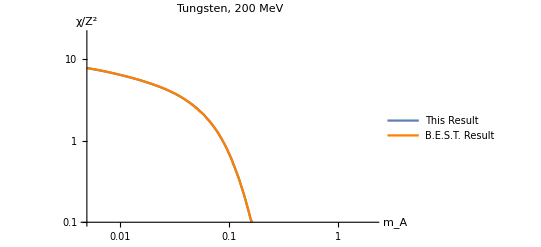

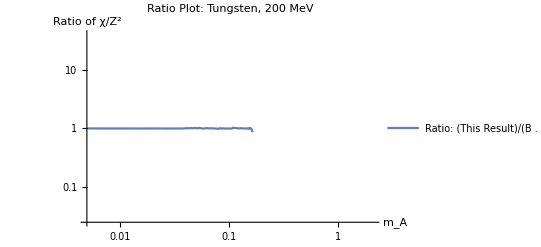

```mathematica
Show[AnTungsten200MeVPlot,BESTTungsten200MeVPlot]
Show[ AnTungsten200MeVRatioPlot]
```

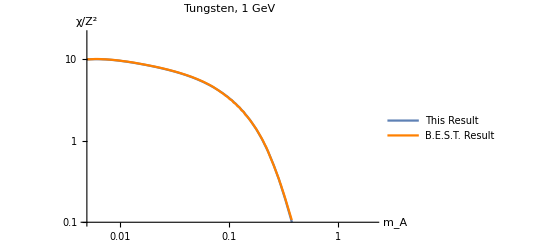

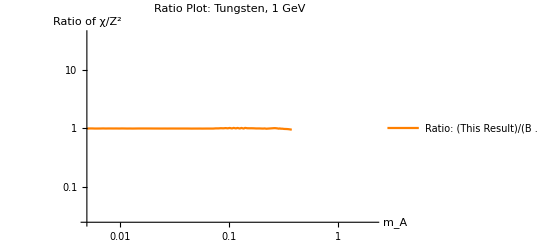

```mathematica
Show[AnTungsten1GeVPlot,BESTTungsten1GeVPlot]
Show[ AnTungsten1GeVRatioPlot]
```

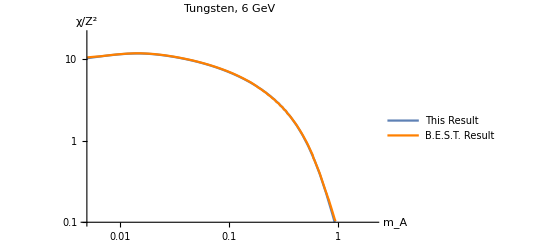

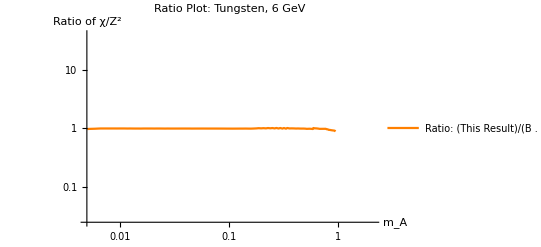

```mathematica
Show[AnTungsten6GeVPlot,BESTTungsten6GeVPlot]
Show[AnTungsten6GeVRatioPlot]
```

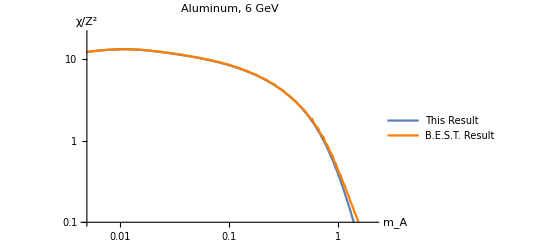

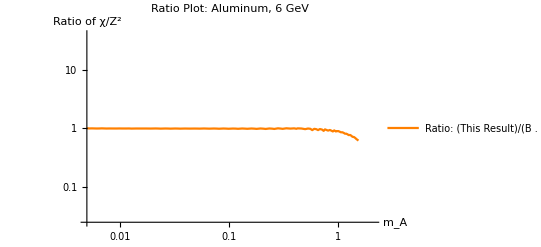

```mathematica
Show[AnAluminum6GeVPlot,BESTAluminum6GeVPlot]
Show[AnAluminum6GeVRatioPlot]
```

#### All Ratio Plots

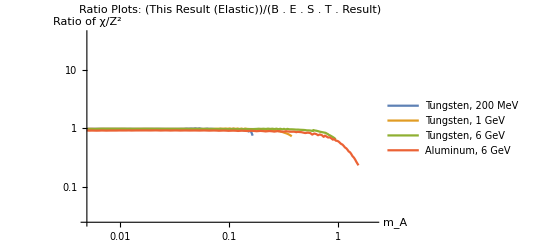

```mathematica
(* Elastic Only *)
Show[ ElAnAllRatioPlots]
```

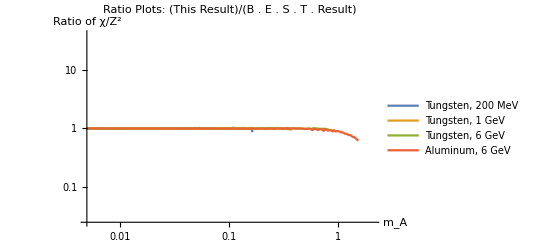

```mathematica
(* Elastic + Inelastic *)
Show[ AnAllRatioPlots]
```